```mathematica
CountryData["UnitedStates","InflationRate"]
```

0.0145036 per year

```mathematica
CountryData["UnitedStates",{"InflationRate",All}]
```

TimeSeries[…]

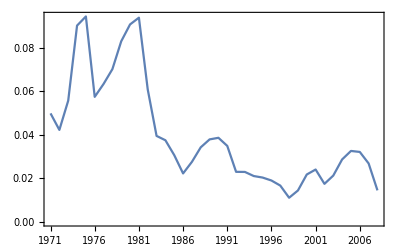

```mathematica
DateListPlot[TimeSeries[…]]
```

```mathematica
Out[2]["Values"]
```

QuantityArray[…]

```mathematica
Normal[%4]
```

{0.0499088 per year,0.0423121 per year,0.0557773 per year,0.0902887 per year,0.0944886 per year,0.0575139 per year,0.0634455 per year,0.0702634 per year,0.0830702 per year,0.0908216 per year,0.0939243 per year,0.0609088 per year,0.0395455 per year,0.0375504 per year,0.0306966 per year,0.0222927 per year,0.0276107 per year,0.0343012 per year,0.0379449 per year,0.0386782 per year,0.0349598 per year,0.0230273 per year,0.0229747 per year,0.0210903 per year,0.0203923 per year,0.0190374 per year,0.0167035 per year,0.0111104 per year,0.0144494 per year,0.0217986 per year,0.0240881 per year,0.0175005 per year,0.0213105 per year,0.0287257 per year,0.0326351 per year,0.0321724 per year,0.0268834 per year,0.0145036 per year}

```mathematica
QuantityMagnitude/@Out[5]
```

{0.0499088,0.0423121,0.0557773,0.0902887,0.0944886,0.0575139,0.0634455,0.0702634,0.0830702,0.0908216,0.0939243,0.0609088,0.0395455,0.0375504,0.0306966,0.0222927,0.0276107,0.0343012,0.0379449,0.0386782,0.0349598,0.0230273,0.0229747,0.0210903,0.0203923,0.0190374,0.0167035,0.0111104,0.0144494,0.0217986,0.0240881,0.0175005,0.0213105,0.0287257,0.0326351,0.0321724,0.0268834,0.0145036}

```mathematica
1+Out[6]
```

{1.04991,1.04231,1.05578,1.09029,1.09449,1.05751,1.06345,1.07026,1.08307,1.09082,1.09392,1.06091,1.03955,1.03755,1.0307,1.02229,1.02761,1.0343,1.03794,1.03868,1.03496,1.02303,1.02297,1.02109,1.02039,1.01904,1.0167,1.01111,1.01445,1.0218,1.02409,1.0175,1.02131,1.02873,1.03264,1.03217,1.02688,1.0145}

```mathematica
1-Out[6]
```

{0.950091,0.957688,0.944223,0.909711,0.905511,0.942486,0.936554,0.929737,0.91693,0.909178,0.906076,0.939091,0.960455,0.96245,0.969303,0.977707,0.972389,0.965699,0.962055,0.961322,0.96504,0.976973,0.977025,0.97891,0.979608,0.980963,0.983296,0.98889,0.985551,0.978201,0.975912,0.9825,0.978689,0.971274,0.967365,0.967828,0.973117,0.985496}

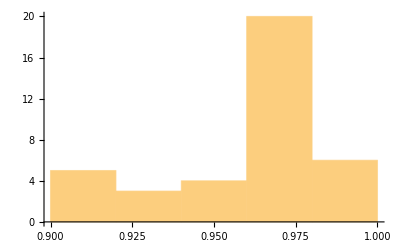

```mathematica
Histogram[%8]
```

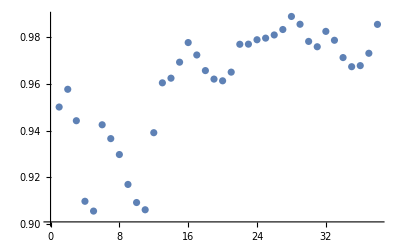

```mathematica
ListPlot[%8]
```

```mathematica
Fold[Times,{1},Out[8]]
```

{0.208362}

```mathematica
GeometricMean@Out[8]
```

0.959565

```mathematica
Fold[Times,{50},Out[8]]
```

{10.4181}

```mathematica
InflationAdjust[Quantity[50,"USDollars"],DatePlus[Today,-10000]]
```

Set::write: Tag InflationAdjust in Options[InflationAdjust] is Protected.

SetDelayed::write: Tag InflationAdjust in InflationAdjust[args___] is Protected.

SetDelayed::write: Tag InflationAdjust in InflationAdjust[(Quantity[q_,DatedUnit[SourceUnit_String]])?QuantityQ,opts:OptionsPattern[]] is Protected.

SetDelayed::write: Tag InflationAdjust in InflationAdjust[(Quantity[q_,DatedUnit[SourceUnit_,SourceDate_?DateListQ]])?QuantityQ,SourceDate_?DateListQ,opts:OptionsPattern[]] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

26.90 $(USDollarsWed 30 Sep 1992)

```mathematica
InflationAdjust[Quantity[50,"USDollars"],DatePlus[Today,-100000]]
```

InflationAdjust::datenc: USDollars unit can only be converted from 1774 to 2020.

Missing[NotAvailable]

```mathematica
InflationAdjust[Quantity[50,"USDollars"],DatePlus[Today,-50000]]
```

1.86 $(USDollarsMon 26 Mar 1883)

```mathematica
DateObject[{1,1,1900}]
```

Day: Wed 15 Mar 6

```mathematica
InflationAdjust[Quantity[50,"USDollars"],DateObject[{6,3,15},"Day","Gregorian",-8.]]
```

InflationAdjust::datenc: USDollars unit can only be converted from 1774 to 2020.

Missing[NotAvailable]

```mathematica
FinancialData["SPXL","Close",{{2019},{2020}}]
```

TimeSeries[…]

```mathematica
FinancialData["VIXY","Close",{{2019},{2020}}]
```

TimeSeries[…]

```mathematica
RandomChoice[{.5,.5}->{1,2}]
```

1

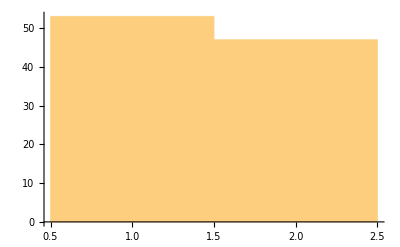

```mathematica
Histogram[RandomChoice[{.5,.5}->{1,2},100]]
```

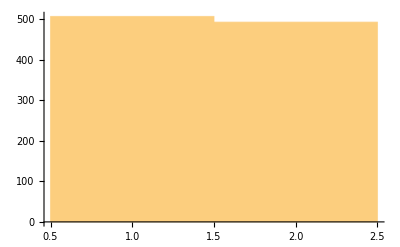

```mathematica
Histogram[RandomChoice[{.5,.5}->{1,2},1000]]
```

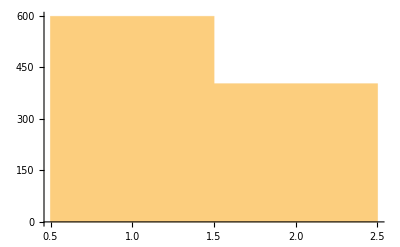

```mathematica
Histogram[RandomChoice[{.6,.4}->{1,2},1000]]
```

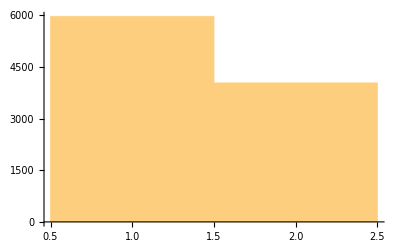

```mathematica
Histogram[RandomChoice[{.6,.4}->{1,2},10000]]
```

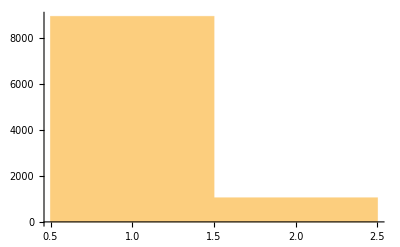

```mathematica
Histogram[RandomChoice[{.9,.1}->{1,2},10000]]
```

```mathematica
Join[
Transpose[{
Out[19]["Dates"][[;;-2]],
Ratios@Out[19]["Values"]
}],
Transpose[{
Out[20]["Dates"][[;;-2]],
Ratios@Out[20]["Values"]
}]
]
```

{{Wed 2 Jan 2019 00:00:00GMT-8.,0.925903},{Thu 3 Jan 2019 00:00:00GMT-8.,1.10102},{Fri 4 Jan 2019 00:00:00GMT-8.,1.02413},{Mon 7 Jan 2019 00:00:00GMT-8.,1.02705},{Tue 8 Jan 2019 00:00:00GMT-8.,1.01473},{Wed 9 Jan 2019 00:00:00GMT-8.,1.01116},552,{Thu 6 Feb 2020 00:00:00GMT-8.,1.01295},{Fri 7 Feb 2020 00:00:00GMT-8.,0.988917},{Mon 10 Feb 2020 00:00:00GMT-8.,1.00172},{Tue 11 Feb 2020 00:00:00GMT-8.,0.951807},{Wed 12 Feb 2020 00:00:00GMT-8.,1.01718},{Thu 13 Feb 2020 00:00:00GMT-8.,0.986667}}
 |  |  |  |

```mathematica
GatherBy[Out[27],First]
```

{{{Wed 2 Jan 2019 00:00:00GMT-8.,0.925903},{Wed 2 Jan 2019 00:00:00GMT-8.,1.04698}},{{Thu 3 Jan 2019 00:00:00GMT-8.,1.10102},{Thu 3 Jan 2019 00:00:00GMT-8.,0.919684}},{{Fri 4 Jan 2019 00:00:00GMT-8.,1.02413},{Fri 4 Jan 2019 00:00:00GMT-8.,0.97893}},276,{{Tue 11 Feb 2020 00:00:00GMT-8.,1.01867},{Tue 11 Feb 2020 00:00:00GMT-8.,0.951807}},{{Wed 12 Feb 2020 00:00:00GMT-8.,0.996946},{Wed 12 Feb 2020 00:00:00GMT-8.,1.01718}},{{Thu 13 Feb 2020 00:00:00GMT-8.,1.00413},{Thu 13 Feb 2020 00:00:00GMT-8.,0.986667}}}
 |  |  |  |

```mathematica
{First@First@#,{Last@First@#,Last@Last@#}}&/@Out[28]
```

{{Wed 2 Jan 2019 00:00:00GMT-8.,{0.925903,1.04698}},{Thu 3 Jan 2019 00:00:00GMT-8.,{1.10102,0.919684}},{Fri 4 Jan 2019 00:00:00GMT-8.,{1.02413,0.97893}},{Mon 7 Jan 2019 00:00:00GMT-8.,{1.02705,0.979043}},{Tue 8 Jan 2019 00:00:00GMT-8.,{1.01473,0.976859}},{Wed 9 Jan 2019 00:00:00GMT-8.,{1.01116,0.989636}},{Thu 10 Jan 2019 00:00:00GMT-8.,{1.00028,0.967385}},{Fri 11 Jan 2019 00:00:00GMT-8.,{0.981788,1.00402}},{Mon 14 Jan 2019 00:00:00GMT-8.,{1.03457,0.955022}},{Tue 15 Jan 2019 00:00:00GMT-8.,{1.0057,1.01806}},{Wed 16 Jan 2019 00:00:00GMT-8.,{1.02404,0.989861}},{Thu 17 Jan 2019 00:00:00GMT-8.,{1.03798,0.974712}},{Fri 18 Jan 2019 00:00:00GMT-8.,{0.960864,1.09163}},{Tue 22 Jan 2019 00:00:00GMT-8.,{1.00397,0.990373}},{Wed 23 Jan 2019 00:00:00GMT-8.,{1.00263,0.967801}},{Thu 24 Jan 2019 00:00:00GMT-8.,{1.02733,0.961601}},{Fri 25 Jan 2019 00:00:00GMT-8.,{0.975448,1.04287}},{Mon 28 Jan 2019 00:00:00GMT-8.,{0.994756,0.996244}},{Tue 29 Jan 2019 00:00:00GMT-8.,{1.04744,0.955388}},{Wed 30 Jan 2019 00:00:00GMT-8.,{1.02667,0.958566}},{Thu 31 Jan 2019 00:00:00GMT-8.,{1.00074,0.990051}},{Fri 1 Feb 2019 00:00:00GMT-8.,{1.02106,0.968468}},{Mon 4 Feb 2019 00:00:00GMT-8.,{1.01247,0.992844}},{Tue 5 Feb 2019 00:00:00GMT-8.,{0.996209,0.992793}},{Wed 6 Feb 2019 00:00:00GMT-8.,{0.970749,1.03485}},{Thu 7 Feb 2019 00:00:00GMT-8.,{1.00294,0.988074}},{Fri 8 Feb 2019 00:00:00GMT-8.,{1.0022,0.98864}},{Mon 11 Feb 2019 00:00:00GMT-8.,{1.03851,0.982047}},{Tue 12 Feb 2019 00:00:00GMT-8.,{1.00868,0.996709}},{Wed 13 Feb 2019 00:00:00GMT-8.,{0.993253,1.01798}},{Thu 14 Feb 2019 00:00:00GMT-8.,{1.03233,0.966126}},{Fri 15 Feb 2019 00:00:00GMT-8.,{1.00522,1.00224}},{Tue 19 Feb 2019 00:00:00GMT-8.,{1.00587,0.961295}},{Wed 20 Feb 2019 00:00:00GMT-8.,{0.989004,1.01007}},{Thu 21 Feb 2019 00:00:00GMT-8.,{1.01906,0.963204}},{Fri 22 Feb 2019 00:00:00GMT-8.,{1.00379,1.0187}},{Mon 25 Feb 2019 00:00:00GMT-8.,{0.99756,1.00898}},{Tue 26 Feb 2019 00:00:00GMT-8.,{0.997776,1.00155}},{Wed 27 Feb 2019 00:00:00GMT-8.,{0.993537,0.998067}},{Thu 28 Feb 2019 00:00:00GMT-8.,{1.01952,0.955461}},{Fri 1 Mar 2019 00:00:00GMT-8.,{0.987679,1.02432}},{Mon 4 Mar 2019 00:00:00GMT-8.,{0.996659,1.00633}},{Tue 5 Mar 2019 00:00:00GMT-8.,{0.980778,1.02556}},{Wed 6 Mar 2019 00:00:00GMT-8.,{0.975843,1.04141}},{Thu 7 Mar 2019 00:00:00GMT-8.,{0.993227,1.00589}},{Fri 8 Mar 2019 00:00:00GMT-8.,{1.04397,0.927526}},{Mon 11 Mar 2019 00:00:00GMT-8.,{1.01059,0.970797}},{Tue 12 Mar 2019 00:00:00GMT-8.,{1.01984,0.989837}},{Wed 13 Mar 2019 00:00:00GMT-8.,{0.997596,0.984394}},{Thu 14 Mar 2019 00:00:00GMT-8.,{1.0149,0.980392}},{Fri 15 Mar 2019 00:00:00GMT-8.,{1.00971,1.00255}},{Mon 18 Mar 2019 00:00:00GMT-8.,{1.00171,1.00806}},{Tue 19 Mar 2019 00:00:00GMT-8.,{0.98997,1.00926}},{Wed 20 Mar 2019 00:00:00GMT-8.,{1.03298,0.984981}},{Thu 21 Mar 2019 00:00:00GMT-8.,{0.942821,1.11605}},{Fri 22 Mar 2019 00:00:00GMT-8.,{0.996459,1.0019}},{Mon 25 Mar 2019 00:00:00GMT-8.,{1.02243,0.946591}},{Tue 26 Mar 2019 00:00:00GMT-8.,{0.98501,1.01521}},{Wed 27 Mar 2019 00:00:00GMT-8.,{1.01169,0.978321}},{Thu 28 Mar 2019 00:00:00GMT-8.,{1.0194,0.967768}},{Fri 29 Mar 2019 00:00:00GMT-8.,{1.03422,0.983347}},{Mon 1 Apr 2019 00:00:00GMT-8.,{1.00103,0.997036}},{Tue 2 Apr 2019 00:00:00GMT-8.,{1.00496,1.00722}},{Wed 3 Apr 2019 00:00:00GMT-8.,{1.0074,0.991568}},{Thu 4 Apr 2019 00:00:00GMT-8.,{1.01326,0.978316}},{Fri 5 Apr 2019 00:00:00GMT-8.,{1.00302,0.995654}},{Mon 8 Apr 2019 00:00:00GMT-8.,{0.983939,1.03536}},{Tue 9 Apr 2019 00:00:00GMT-8.,{1.0102,0.973019}},{Wed 10 Apr 2019 00:00:00GMT-8.,{0.999192,0.97877}},{Thu 11 Apr 2019 00:00:00GMT-8.,{1.01981,0.953962}},{Fri 12 Apr 2019 00:00:00GMT-8.,{0.998018,0.988399}},{Mon 15 Apr 2019 00:00:00GMT-8.,{1.00159,0.993427}},{Tue 16 Apr 2019 00:00:00GMT-8.,{0.992068,1.00567}},{Wed 17 Apr 2019 00:00:00GMT-8.,{1.0054,0.983553}},{Thu 18 Apr 2019 00:00:00GMT-8.,{1.00179,0.991878}},{Mon 22 Apr 2019 00:00:00GMT-8.,{1.02699,0.991329}},{Tue 23 Apr 2019 00:00:00GMT-8.,{0.994783,1.02381}},{Wed 24 Apr 2019 00:00:00GMT-8.,{0.997281,1.02041}},{Thu 25 Apr 2019 00:00:00GMT-8.,{1.01325,0.967442}},{Fri 26 Apr 2019 00:00:00GMT-8.,{1.00346,1.01394}},{Mon 29 Apr 2019 00:00:00GMT-8.,{1.00192,1.00142}},{Tue 30 Apr 2019 00:00:00GMT-8.,{0.978012,1.03693}},{Wed 1 May 2019 00:00:00GMT-8.,{0.993157,1.00137}},{Thu 2 May 2019 00:00:00GMT-8.,{1.02854,0.952576}},{Fri 3 May 2019 00:00:00GMT-8.,{0.988325,1.05361}},{Mon 6 May 2019 00:00:00GMT-8.,{0.950039,1.16765}},{Tue 7 May 2019 00:00:00GMT-8.,{0.995312,0.980545}},{Wed 8 May 2019 00:00:00GMT-8.,{0.992218,0.998809}},{Thu 9 May 2019 00:00:00GMT-8.,{1.01073,0.922527}},{Fri 10 May 2019 00:00:00GMT-8.,{0.926281,1.14599}},{Mon 13 May 2019 00:00:00GMT-8.,{1.02535,0.946261}},{Tue 14 May 2019 00:00:00GMT-8.,{1.01763,0.958697}},{Wed 15 May 2019 00:00:00GMT-8.,{1.02726,0.957747}},{Thu 16 May 2019 00:00:00GMT-8.,{0.981695,1.01384}},{Fri 17 May 2019 00:00:00GMT-8.,{0.979258,1.01493}},{Mon 20 May 2019 00:00:00GMT-8.,{1.02674,0.950399}},{Tue 21 May 2019 00:00:00GMT-8.,{0.991248,0.988943}},{Wed 22 May 2019 00:00:00GMT-8.,{0.964684,1.06619}},{Thu 23 May 2019 00:00:00GMT-8.,{1.0037,0.979866}},{Fri 24 May 2019 00:00:00GMT-8.,{0.972644,1.02954}},{Tue 28 May 2019 00:00:00GMT-8.,{0.979464,1.01996}},{Wed 29 May 2019 00:00:00GMT-8.,{1.00843,0.979209}},{Thu 30 May 2019 00:00:00GMT-8.,{0.960904,1.04371}},{Fri 31 May 2019 00:00:00GMT-8.,{0.990122,1.00638}},{Mon 3 Jun 2019 00:00:00GMT-8.,{1.06485,0.946096}},{Tue 4 Jun 2019 00:00:00GMT-8.,{1.02588,0.978634}},{Wed 5 Jun 2019 00:00:00GMT-8.,{1.01957,0.980308}},{Thu 6 Jun 2019 00:00:00GMT-8.,{1.02922,1.0083}},{Fri 7 Jun 2019 00:00:00GMT-8.,{1.01347,0.990039}},{Mon 10 Jun 2019 00:00:00GMT-8.,{0.999387,1.0035}},{Tue 11 Jun 2019 00:00:00GMT-8.,{0.994885,0.993897}},{Wed 12 Jun 2019 00:00:00GMT-8.,{1.01254,0.995614}},{Thu 13 Jun 2019 00:00:00GMT-8.,{0.995329,0.990308}},{Fri 14 Jun 2019 00:00:00GMT-8.,{1.00204,0.988434}},{Mon 17 Jun 2019 00:00:00GMT-8.,{1.02912,0.992349}},{Tue 18 Jun 2019 00:00:00GMT-8.,{1.0089,0.965533}},{Wed 19 Jun 2019 00:00:00GMT-8.,{1.02785,1.0047}},{Thu 20 Jun 2019 00:00:00GMT-8.,{0.99523,1.02384}},{Fri 21 Jun 2019 00:00:00GMT-8.,{0.996166,0.989954}},{Mon 24 Jun 2019 00:00:00GMT-8.,{0.964396,1.02721}},{Tue 25 Jun 2019 00:00:00GMT-8.,{0.997805,0.99057}},{Wed 26 Jun 2019 00:00:00GMT-8.,{1.0094,0.983228}},{Thu 27 Jun 2019 00:00:00GMT-8.,{1.01744,0.98663}},{Fri 28 Jun 2019 00:00:00GMT-8.,{1.02356,0.942523}},{Mon 1 Jul 2019 00:00:00GMT-8.,{1.00913,0.962816}},{Tue 2 Jul 2019 00:00:00GMT-8.,{1.02244,0.994851}},{Wed 3 Jul 2019 00:00:00GMT-8.,{0.995574,1.00362}},{Fri 5 Jul 2019 00:00:00GMT-8.,{0.985923,1.02682}},{Mon 8 Jul 2019 00:00:00GMT-8.,{1.00282,1.00402}},{Tue 9 Jul 2019 00:00:00GMT-8.,{1.01442,0.968985}},{Wed 10 Jul 2019 00:00:00GMT-8.,{1.00591,0.982963}},{Thu 11 Jul 2019 00:00:00GMT-8.,{1.01267,0.982143}},{Fri 12 Jul 2019 00:00:00GMT-8.,{1.00127,0.999465}},{Mon 15 Jul 2019 00:00:00GMT-8.,{0.989317,1.00321}},{Tue 16 Jul 2019 00:00:00GMT-8.,{0.981149,1.02293}},{Wed 17 Jul 2019 00:00:00GMT-8.,{1.01045,0.991137}},{Thu 18 Jul 2019 00:00:00GMT-8.,{0.981724,1.01105}},{Fri 19 Jul 2019 00:00:00GMT-8.,{1.00752,0.979188}},{Mon 22 Jul 2019 00:00:00GMT-8.,{1.02146,0.965994}},{Tue 23 Jul 2019 00:00:00GMT-8.,{1.01407,0.973597}},{Wed 24 Jul 2019 00:00:00GMT-8.,{0.984865,1.03164}},{Thu 25 Jul 2019 00:00:00GMT-8.,{1.01976,0.974808}},{Fri 26 Jul 2019 00:00:00GMT-8.,{0.994977,1.00674}},{Mon 29 Jul 2019 00:00:00GMT-8.,{0.993509,1.02511}},{Tue 30 Jul 2019 00:00:00GMT-8.,{0.965336,1.05607}},{Wed 31 Jul 2019 00:00:00GMT-8.,{0.974243,1.07732}},{Thu 1 Aug 2019 00:00:00GMT-8.,{0.977808,1.00718}},{Fri 2 Aug 2019 00:00:00GMT-8.,{0.910401,1.14727}},{Mon 5 Aug 2019 00:00:00GMT-8.,{1.04054,0.936646}},{Tue 6 Aug 2019 00:00:00GMT-8.,{1.00188,1.00442}},{Wed 7 Aug 2019 00:00:00GMT-8.,{1.05718,0.939701}},{Thu 8 Aug 2019 00:00:00GMT-8.,{0.978167,1.03747}},{Fri 9 Aug 2019 00:00:00GMT-8.,{0.964408,1.07269}},{Mon 12 Aug 2019 00:00:00GMT-8.,{1.04691,0.925084}},{Tue 13 Aug 2019 00:00:00GMT-8.,{0.910775,1.14013}},{Wed 14 Aug 2019 00:00:00GMT-8.,{1.00809,0.975259}},{Thu 15 Aug 2019 00:00:00GMT-8.,{1.04295,0.944353}},{Fri 16 Aug 2019 00:00:00GMT-8.,{1.03598,0.925043}},{Mon 19 Aug 2019 00:00:00GMT-8.,{0.977314,1.02389}},{Tue 20 Aug 2019 00:00:00GMT-8.,{1.02465,0.952424}},{Wed 21 Aug 2019 00:00:00GMT-8.,{0.997795,1.01585}},{Thu 22 Aug 2019 00:00:00GMT-8.,{0.92385,1.12435}},{Fri 23 Aug 2019 00:00:00GMT-8.,{1.03241,0.973507}},{Mon 26 Aug 2019 00:00:00GMT-8.,{0.987992,1.01814}},{Tue 27 Aug 2019 00:00:00GMT-8.,{1.02111,0.97709}},{Wed 28 Aug 2019 00:00:00GMT-8.,{1.03738,0.959618}},{Thu 29 Aug 2019 00:00:00GMT-8.,{0.999195,1.0009}},{Fri 30 Aug 2019 00:00:00GMT-8.,{0.982675,1.05018}},{Tue 3 Sep 2019 00:00:00GMT-8.,{1.03239,0.93672}},{Wed 4 Sep 2019 00:00:00GMT-8.,{1.03892,0.960937}},{Thu 5 Sep 2019 00:00:00GMT-8.,{1.00229,0.97274}},{Fri 6 Sep 2019 00:00:00GMT-8.,{1.00038,0.989184}},{Mon 9 Sep 2019 00:00:00GMT-8.,{1.00114,0.999006}},{Tue 10 Sep 2019 00:00:00GMT-8.,{1.02094,0.980597}},{Wed 11 Sep 2019 00:00:00GMT-8.,{1.00895,0.976154}},{Thu 12 Sep 2019 00:00:00GMT-8.,{0.997412,0.984927}},{Fri 13 Sep 2019 00:00:00GMT-8.,{0.991475,1.01583}},{Mon 16 Sep 2019 00:00:00GMT-8.,{1.00654,0.995844}},{Tue 17 Sep 2019 00:00:00GMT-8.,{1.00223,0.966615}},{Wed 18 Sep 2019 00:00:00GMT-8.,{0.999629,0.982731}},{Thu 19 Sep 2019 00:00:00GMT-8.,{0.983503,1.04833}},{Fri 20 Sep 2019 00:00:00GMT-8.,{1.00151,0.993714}},{Mon 23 Sep 2019 00:00:00GMT-8.,{0.975348,1.04639}},{Tue 24 Sep 2019 00:00:00GMT-8.,{1.01833,0.978338}},{Wed 25 Sep 2019 00:00:00GMT-8.,{0.9928,1.00669}},{Thu 26 Sep 2019 00:00:00GMT-8.,{0.983206,1.02762}},{Fri 27 Sep 2019 00:00:00GMT-8.,{1.01533,0.971628}},{Mon 30 Sep 2019 00:00:00GMT-8.,{0.963296,1.04355}},{Tue 1 Oct 2019 00:00:00GMT-8.,{0.948204,1.06775}},{Wed 2 Oct 2019 00:00:00GMT-8.,{1.0226,0.962759}},{Thu 3 Oct 2019 00:00:00GMT-8.,{1.04011,0.945081}},{Fri 4 Oct 2019 00:00:00GMT-8.,{0.986619,1.01061}},{Mon 7 Oct 2019 00:00:00GMT-8.,{0.954926,1.0795}},{Tue 8 Oct 2019 00:00:00GMT-8.,{1.02611,0.962946}},{Wed 9 Oct 2019 00:00:00GMT-8.,{1.02198,0.967773}},{Thu 10 Oct 2019 00:00:00GMT-8.,{1.03027,0.942843}},{Fri 11 Oct 2019 00:00:00GMT-8.,{0.997294,0.965735}},{Mon 14 Oct 2019 00:00:00GMT-8.,{1.02908,0.972162}},{Tue 15 Oct 2019 00:00:00GMT-8.,{0.994726,0.987086}},{Wed 16 Oct 2019 00:00:00GMT-8.,{1.0072,0.995449}},{Thu 17 Oct 2019 00:00:00GMT-8.,{0.987028,0.998286}},{Fri 18 Oct 2019 00:00:00GMT-8.,{1.02171,0.973097}},{Mon 21 Oct 2019 00:00:00GMT-8.,{0.988628,1.01529}},{Tue 22 Oct 2019 00:00:00GMT-8.,{1.00943,0.987833}},{Wed 23 Oct 2019 00:00:00GMT-8.,{1.00374,0.98651}},{Thu 24 Oct 2019 00:00:00GMT-8.,{1.01359,0.966112}},{Fri 25 Oct 2019 00:00:00GMT-8.,{1.01598,1.01108}},{Mon 28 Oct 2019 00:00:00GMT-8.,{0.998373,0.999391}},{Tue 29 Oct 2019 00:00:00GMT-8.,{1.00905,0.974421}},{Wed 30 Oct 2019 00:00:00GMT-8.,{0.99103,1.01625}},{Thu 31 Oct 2019 00:00:00GMT-8.,{1.02824,0.95449}},{Fri 1 Nov 2019 00:00:00GMT-8.,{1.01144,1.00258}},{Mon 4 Nov 2019 00:00:00GMT-8.,{0.996693,1.01992}},{Tue 5 Nov 2019 00:00:00GMT-8.,{1.00122,0.995589}},{Wed 6 Nov 2019 00:00:00GMT-8.,{1.01081,0.990506}},{Thu 7 Nov 2019 00:00:00GMT-8.,{1.00587,0.978914}},{Fri 8 Nov 2019 00:00:00GMT-8.,{0.994339,0.997389}},{Mon 11 Nov 2019 00:00:00GMT-8.,{1.00569,0.98822}},{Tue 12 Nov 2019 00:00:00GMT-8.,{1.00137,1.00662}},{Wed 13 Nov 2019 00:00:00GMT-8.,{1.00463,0.984868}},{Thu 14 Nov 2019 00:00:00GMT-8.,{1.02149,0.95658}},{Fri 15 Nov 2019 00:00:00GMT-8.,{1.00083,0.998603}},{Mon 18 Nov 2019 00:00:00GMT-8.,{0.999166,1.01049}},{Tue 19 Nov 2019 00:00:00GMT-8.,{0.989482,1.00969}},{Wed 20 Nov 2019 00:00:00GMT-8.,{0.995276,1.00206}},{Thu 21 Nov 2019 00:00:00GMT-8.,{1.00576,0.971272}},{Fri 22 Nov 2019 00:00:00GMT-8.,{1.02292,0.955634}},{Mon 25 Nov 2019 00:00:00GMT-8.,{1.00659,0.986735}},{Tue 26 Nov 2019 00:00:00GMT-8.,{1.01293,0.995519}},{Wed 27 Nov 2019 00:00:00GMT-8.,{0.989334,1.0165}},{Fri 29 Nov 2019 00:00:00GMT-8.,{0.973701,1.05609}},{Mon 2 Dec 2019 00:00:00GMT-8.,{0.979366,1.0573}},{Tue 3 Dec 2019 00:00:00GMT-8.,{1.0185,0.953734}},{Wed 4 Dec 2019 00:00:00GMT-8.,{1.00673,0.987526}},{Thu 5 Dec 2019 00:00:00GMT-8.,{1.02589,0.966316}},{Fri 6 Dec 2019 00:00:00GMT-8.,{0.99137,1.05084}},{Mon 9 Dec 2019 00:00:00GMT-8.,{0.996386,1.00069}},{Tue 10 Dec 2019 00:00:00GMT-8.,{1.00841,0.979972}},{Wed 11 Dec 2019 00:00:00GMT-8.,{1.02567,0.942918}},{Thu 12 Dec 2019 00:00:00GMT-8.,{1.00096,0.955157}},{Fri 13 Dec 2019 00:00:00GMT-8.,{1.02086,0.977308}},{Mon 16 Dec 2019 00:00:00GMT-8.,{1.00031,0.991994}},{Tue 17 Dec 2019 00:00:00GMT-8.,{1.,1.0113}},{Wed 18 Dec 2019 00:00:00GMT-8.,{1.01263,0.975259}},{Thu 19 Dec 2019 00:00:00GMT-8.,{1.01463,1.01064}},{Fri 20 Dec 2019 00:00:00GMT-8.,{0.998027,1.00486}},{Mon 23 Dec 2019 00:00:00GMT-8.,{1.0003,0.989525}},{Tue 24 Dec 2019 00:00:00GMT-8.,{1.0152,0.997557}},{Thu 26 Dec 2019 00:00:00GMT-8.,{0.999401,1.02204}},{Fri 27 Dec 2019 00:00:00GMT-8.,{0.982469,1.03594}},{Mon 30 Dec 2019 00:00:00GMT-8.,{1.00778,0.958365}},{Tue 31 Dec 2019 00:00:00GMT-8.,{1.02769,0.961384}},{Thu 2 Jan 2020 00:00:00GMT-8.,{0.975998,1.05021}},{Fri 3 Jan 2020 00:00:00GMT-8.,{1.01162,0.988048}},{Mon 6 Jan 2020 00:00:00GMT-8.,{0.992394,0.995968}},{Tue 7 Jan 2020 00:00:00GMT-8.,{1.01533,0.980567}},{Wed 8 Jan 2020 00:00:00GMT-8.,{1.02028,0.964162}},{Thu 9 Jan 2020 00:00:00GMT-8.,{0.99057,0.994347}},{Fri 10 Jan 2020 00:00:00GMT-8.,{1.02168,0.973299}},{Mon 13 Jan 2020 00:00:00GMT-8.,{0.994553,0.99469}},{Tue 14 Jan 2020 00:00:00GMT-8.,{1.00706,0.995552}},{Wed 15 Jan 2020 00:00:00GMT-8.,{1.02347,0.976765}},{Thu 16 Jan 2020 00:00:00GMT-8.,{1.01035,1.00274}},{Fri 17 Jan 2020 00:00:00GMT-8.,{0.992803,1.00639}},{Tue 21 Jan 2020 00:00:00GMT-8.,{1.00153,1.00635}},{Wed 22 Jan 2020 00:00:00GMT-8.,{1.00264,0.997297}},{Thu 23 Jan 2020 00:00:00GMT-8.,{0.972512,1.05781}},{Fri 24 Jan 2020 00:00:00GMT-8.,{0.952177,1.10333}},{Mon 27 Jan 2020 00:00:00GMT-8.,{1.03058,0.943498}},{Tue 28 Jan 2020 00:00:00GMT-8.,{0.998254,1.00082}},{Wed 29 Jan 2020 00:00:00GMT-8.,{1.00933,0.984426}},{Thu 30 Jan 2020 00:00:00GMT-8.,{0.945712,1.11324}},{Fri 31 Jan 2020 00:00:00GMT-8.,{1.02122,0.962603}},{Mon 3 Feb 2020 00:00:00GMT-8.,{1.04664,0.94561}},{Tue 4 Feb 2020 00:00:00GMT-8.,{1.03342,0.960559}},{Wed 5 Feb 2020 00:00:00GMT-8.,{1.01078,0.99059}},{Thu 6 Feb 2020 00:00:00GMT-8.,{0.983317,1.01295}},{Fri 7 Feb 2020 00:00:00GMT-8.,{1.02169,0.988917}},{Mon 10 Feb 2020 00:00:00GMT-8.,{1.00612,1.00172}},{Tue 11 Feb 2020 00:00:00GMT-8.,{1.01867,0.951807}},{Wed 12 Feb 2020 00:00:00GMT-8.,{0.996946,1.01718}},{Thu 13 Feb 2020 00:00:00GMT-8.,{1.00413,0.986667}}}

```mathematica
{Last@First@#,Last@Last@#}&/@Out[28]
```

{{0.925903,1.04698},{1.10102,0.919684},{1.02413,0.97893},{1.02705,0.979043},{1.01473,0.976859},{1.01116,0.989636},{1.00028,0.967385},{0.981788,1.00402},{1.03457,0.955022},{1.0057,1.01806},{1.02404,0.989861},{1.03798,0.974712},{0.960864,1.09163},{1.00397,0.990373},{1.00263,0.967801},{1.02733,0.961601},{0.975448,1.04287},{0.994756,0.996244},{1.04744,0.955388},{1.02667,0.958566},{1.00074,0.990051},{1.02106,0.968468},{1.01247,0.992844},{0.996209,0.992793},{0.970749,1.03485},{1.00294,0.988074},{1.0022,0.98864},{1.03851,0.982047},{1.00868,0.996709},{0.993253,1.01798},{1.03233,0.966126},{1.00522,1.00224},{1.00587,0.961295},{0.989004,1.01007},{1.01906,0.963204},{1.00379,1.0187},{0.99756,1.00898},{0.997776,1.00155},{0.993537,0.998067},{1.01952,0.955461},{0.987679,1.02432},{0.996659,1.00633},{0.980778,1.02556},{0.975843,1.04141},{0.993227,1.00589},{1.04397,0.927526},{1.01059,0.970797},{1.01984,0.989837},{0.997596,0.984394},{1.0149,0.980392},{1.00971,1.00255},{1.00171,1.00806},{0.98997,1.00926},{1.03298,0.984981},{0.942821,1.11605},{0.996459,1.0019},{1.02243,0.946591},{0.98501,1.01521},{1.01169,0.978321},{1.0194,0.967768},{1.03422,0.983347},{1.00103,0.997036},{1.00496,1.00722},{1.0074,0.991568},{1.01326,0.978316},{1.00302,0.995654},{0.983939,1.03536},{1.0102,0.973019},{0.999192,0.97877},{1.01981,0.953962},{0.998018,0.988399},{1.00159,0.993427},{0.992068,1.00567},{1.0054,0.983553},{1.00179,0.991878},{1.02699,0.991329},{0.994783,1.02381},{0.997281,1.02041},{1.01325,0.967442},{1.00346,1.01394},{1.00192,1.00142},{0.978012,1.03693},{0.993157,1.00137},{1.02854,0.952576},{0.988325,1.05361},{0.950039,1.16765},{0.995312,0.980545},{0.992218,0.998809},{1.01073,0.922527},{0.926281,1.14599},{1.02535,0.946261},{1.01763,0.958697},{1.02726,0.957747},{0.981695,1.01384},{0.979258,1.01493},{1.02674,0.950399},{0.991248,0.988943},{0.964684,1.06619},{1.0037,0.979866},{0.972644,1.02954},{0.979464,1.01996},{1.00843,0.979209},{0.960904,1.04371},{0.990122,1.00638},{1.06485,0.946096},{1.02588,0.978634},{1.01957,0.980308},{1.02922,1.0083},{1.01347,0.990039},{0.999387,1.0035},{0.994885,0.993897},{1.01254,0.995614},{0.995329,0.990308},{1.00204,0.988434},{1.02912,0.992349},{1.0089,0.965533},{1.02785,1.0047},{0.99523,1.02384},{0.996166,0.989954},{0.964396,1.02721},{0.997805,0.99057},{1.0094,0.983228},{1.01744,0.98663},{1.02356,0.942523},{1.00913,0.962816},{1.02244,0.994851},{0.995574,1.00362},{0.985923,1.02682},{1.00282,1.00402},{1.01442,0.968985},{1.00591,0.982963},{1.01267,0.982143},{1.00127,0.999465},{0.989317,1.00321},{0.981149,1.02293},{1.01045,0.991137},{0.981724,1.01105},{1.00752,0.979188},{1.02146,0.965994},{1.01407,0.973597},{0.984865,1.03164},{1.01976,0.974808},{0.994977,1.00674},{0.993509,1.02511},{0.965336,1.05607},{0.974243,1.07732},{0.977808,1.00718},{0.910401,1.14727},{1.04054,0.936646},{1.00188,1.00442},{1.05718,0.939701},{0.978167,1.03747},{0.964408,1.07269},{1.04691,0.925084},{0.910775,1.14013},{1.00809,0.975259},{1.04295,0.944353},{1.03598,0.925043},{0.977314,1.02389},{1.02465,0.952424},{0.997795,1.01585},{0.92385,1.12435},{1.03241,0.973507},{0.987992,1.01814},{1.02111,0.97709},{1.03738,0.959618},{0.999195,1.0009},{0.982675,1.05018},{1.03239,0.93672},{1.03892,0.960937},{1.00229,0.97274},{1.00038,0.989184},{1.00114,0.999006},{1.02094,0.980597},{1.00895,0.976154},{0.997412,0.984927},{0.991475,1.01583},{1.00654,0.995844},{1.00223,0.966615},{0.999629,0.982731},{0.983503,1.04833},{1.00151,0.993714},{0.975348,1.04639},{1.01833,0.978338},{0.9928,1.00669},{0.983206,1.02762},{1.01533,0.971628},{0.963296,1.04355},{0.948204,1.06775},{1.0226,0.962759},{1.04011,0.945081},{0.986619,1.01061},{0.954926,1.0795},{1.02611,0.962946},{1.02198,0.967773},{1.03027,0.942843},{0.997294,0.965735},{1.02908,0.972162},{0.994726,0.987086},{1.0072,0.995449},{0.987028,0.998286},{1.02171,0.973097},{0.988628,1.01529},{1.00943,0.987833},{1.00374,0.98651},{1.01359,0.966112},{1.01598,1.01108},{0.998373,0.999391},{1.00905,0.974421},{0.99103,1.01625},{1.02824,0.95449},{1.01144,1.00258},{0.996693,1.01992},{1.00122,0.995589},{1.01081,0.990506},{1.00587,0.978914},{0.994339,0.997389},{1.00569,0.98822},{1.00137,1.00662},{1.00463,0.984868},{1.02149,0.95658},{1.00083,0.998603},{0.999166,1.01049},{0.989482,1.00969},{0.995276,1.00206},{1.00576,0.971272},{1.02292,0.955634},{1.00659,0.986735},{1.01293,0.995519},{0.989334,1.0165},{0.973701,1.05609},{0.979366,1.0573},{1.0185,0.953734},{1.00673,0.987526},{1.02589,0.966316},{0.99137,1.05084},{0.996386,1.00069},{1.00841,0.979972},{1.02567,0.942918},{1.00096,0.955157},{1.02086,0.977308},{1.00031,0.991994},{1.,1.0113},{1.01263,0.975259},{1.01463,1.01064},{0.998027,1.00486},{1.0003,0.989525},{1.0152,0.997557},{0.999401,1.02204},{0.982469,1.03594},{1.00778,0.958365},{1.02769,0.961384},{0.975998,1.05021},{1.01162,0.988048},{0.992394,0.995968},{1.01533,0.980567},{1.02028,0.964162},{0.99057,0.994347},{1.02168,0.973299},{0.994553,0.99469},{1.00706,0.995552},{1.02347,0.976765},{1.01035,1.00274},{0.992803,1.00639},{1.00153,1.00635},{1.00264,0.997297},{0.972512,1.05781},{0.952177,1.10333},{1.03058,0.943498},{0.998254,1.00082},{1.00933,0.984426},{0.945712,1.11324},{1.02122,0.962603},{1.04664,0.94561},{1.03342,0.960559},{1.01078,0.99059},{0.983317,1.01295},{1.02169,0.988917},{1.00612,1.00172},{1.01867,0.951807},{0.996946,1.01718},{1.00413,0.986667}}

```mathematica
data=Out[30]
```

{{0.925903,1.04698},{1.10102,0.919684},{1.02413,0.97893},{1.02705,0.979043},{1.01473,0.976859},{1.01116,0.989636},{1.00028,0.967385},{0.981788,1.00402},{1.03457,0.955022},{1.0057,1.01806},{1.02404,0.989861},{1.03798,0.974712},{0.960864,1.09163},{1.00397,0.990373},{1.00263,0.967801},{1.02733,0.961601},{0.975448,1.04287},{0.994756,0.996244},{1.04744,0.955388},{1.02667,0.958566},{1.00074,0.990051},{1.02106,0.968468},{1.01247,0.992844},{0.996209,0.992793},{0.970749,1.03485},{1.00294,0.988074},{1.0022,0.98864},{1.03851,0.982047},{1.00868,0.996709},{0.993253,1.01798},{1.03233,0.966126},{1.00522,1.00224},{1.00587,0.961295},{0.989004,1.01007},{1.01906,0.963204},{1.00379,1.0187},{0.99756,1.00898},{0.997776,1.00155},{0.993537,0.998067},{1.01952,0.955461},{0.987679,1.02432},{0.996659,1.00633},{0.980778,1.02556},{0.975843,1.04141},{0.993227,1.00589},{1.04397,0.927526},{1.01059,0.970797},{1.01984,0.989837},{0.997596,0.984394},{1.0149,0.980392},{1.00971,1.00255},{1.00171,1.00806},{0.98997,1.00926},{1.03298,0.984981},{0.942821,1.11605},{0.996459,1.0019},{1.02243,0.946591},{0.98501,1.01521},{1.01169,0.978321},{1.0194,0.967768},{1.03422,0.983347},{1.00103,0.997036},{1.00496,1.00722},{1.0074,0.991568},{1.01326,0.978316},{1.00302,0.995654},{0.983939,1.03536},{1.0102,0.973019},{0.999192,0.97877},{1.01981,0.953962},{0.998018,0.988399},{1.00159,0.993427},{0.992068,1.00567},{1.0054,0.983553},{1.00179,0.991878},{1.02699,0.991329},{0.994783,1.02381},{0.997281,1.02041},{1.01325,0.967442},{1.00346,1.01394},{1.00192,1.00142},{0.978012,1.03693},{0.993157,1.00137},{1.02854,0.952576},{0.988325,1.05361},{0.950039,1.16765},{0.995312,0.980545},{0.992218,0.998809},{1.01073,0.922527},{0.926281,1.14599},{1.02535,0.946261},{1.01763,0.958697},{1.02726,0.957747},{0.981695,1.01384},{0.979258,1.01493},{1.02674,0.950399},{0.991248,0.988943},{0.964684,1.06619},{1.0037,0.979866},{0.972644,1.02954},{0.979464,1.01996},{1.00843,0.979209},{0.960904,1.04371},{0.990122,1.00638},{1.06485,0.946096},{1.02588,0.978634},{1.01957,0.980308},{1.02922,1.0083},{1.01347,0.990039},{0.999387,1.0035},{0.994885,0.993897},{1.01254,0.995614},{0.995329,0.990308},{1.00204,0.988434},{1.02912,0.992349},{1.0089,0.965533},{1.02785,1.0047},{0.99523,1.02384},{0.996166,0.989954},{0.964396,1.02721},{0.997805,0.99057},{1.0094,0.983228},{1.01744,0.98663},{1.02356,0.942523},{1.00913,0.962816},{1.02244,0.994851},{0.995574,1.00362},{0.985923,1.02682},{1.00282,1.00402},{1.01442,0.968985},{1.00591,0.982963},{1.01267,0.982143},{1.00127,0.999465},{0.989317,1.00321},{0.981149,1.02293},{1.01045,0.991137},{0.981724,1.01105},{1.00752,0.979188},{1.02146,0.965994},{1.01407,0.973597},{0.984865,1.03164},{1.01976,0.974808},{0.994977,1.00674},{0.993509,1.02511},{0.965336,1.05607},{0.974243,1.07732},{0.977808,1.00718},{0.910401,1.14727},{1.04054,0.936646},{1.00188,1.00442},{1.05718,0.939701},{0.978167,1.03747},{0.964408,1.07269},{1.04691,0.925084},{0.910775,1.14013},{1.00809,0.975259},{1.04295,0.944353},{1.03598,0.925043},{0.977314,1.02389},{1.02465,0.952424},{0.997795,1.01585},{0.92385,1.12435},{1.03241,0.973507},{0.987992,1.01814},{1.02111,0.97709},{1.03738,0.959618},{0.999195,1.0009},{0.982675,1.05018},{1.03239,0.93672},{1.03892,0.960937},{1.00229,0.97274},{1.00038,0.989184},{1.00114,0.999006},{1.02094,0.980597},{1.00895,0.976154},{0.997412,0.984927},{0.991475,1.01583},{1.00654,0.995844},{1.00223,0.966615},{0.999629,0.982731},{0.983503,1.04833},{1.00151,0.993714},{0.975348,1.04639},{1.01833,0.978338},{0.9928,1.00669},{0.983206,1.02762},{1.01533,0.971628},{0.963296,1.04355},{0.948204,1.06775},{1.0226,0.962759},{1.04011,0.945081},{0.986619,1.01061},{0.954926,1.0795},{1.02611,0.962946},{1.02198,0.967773},{1.03027,0.942843},{0.997294,0.965735},{1.02908,0.972162},{0.994726,0.987086},{1.0072,0.995449},{0.987028,0.998286},{1.02171,0.973097},{0.988628,1.01529},{1.00943,0.987833},{1.00374,0.98651},{1.01359,0.966112},{1.01598,1.01108},{0.998373,0.999391},{1.00905,0.974421},{0.99103,1.01625},{1.02824,0.95449},{1.01144,1.00258},{0.996693,1.01992},{1.00122,0.995589},{1.01081,0.990506},{1.00587,0.978914},{0.994339,0.997389},{1.00569,0.98822},{1.00137,1.00662},{1.00463,0.984868},{1.02149,0.95658},{1.00083,0.998603},{0.999166,1.01049},{0.989482,1.00969},{0.995276,1.00206},{1.00576,0.971272},{1.02292,0.955634},{1.00659,0.986735},{1.01293,0.995519},{0.989334,1.0165},{0.973701,1.05609},{0.979366,1.0573},{1.0185,0.953734},{1.00673,0.987526},{1.02589,0.966316},{0.99137,1.05084},{0.996386,1.00069},{1.00841,0.979972},{1.02567,0.942918},{1.00096,0.955157},{1.02086,0.977308},{1.00031,0.991994},{1.,1.0113},{1.01263,0.975259},{1.01463,1.01064},{0.998027,1.00486},{1.0003,0.989525},{1.0152,0.997557},{0.999401,1.02204},{0.982469,1.03594},{1.00778,0.958365},{1.02769,0.961384},{0.975998,1.05021},{1.01162,0.988048},{0.992394,0.995968},{1.01533,0.980567},{1.02028,0.964162},{0.99057,0.994347},{1.02168,0.973299},{0.994553,0.99469},{1.00706,0.995552},{1.02347,0.976765},{1.01035,1.00274},{0.992803,1.00639},{1.00153,1.00635},{1.00264,0.997297},{0.972512,1.05781},{0.952177,1.10333},{1.03058,0.943498},{0.998254,1.00082},{1.00933,0.984426},{0.945712,1.11324},{1.02122,0.962603},{1.04664,0.94561},{1.03342,0.960559},{1.01078,0.99059},{0.983317,1.01295},{1.02169,0.988917},{1.00612,1.00172},{1.01867,0.951807},{0.996946,1.01718},{1.00413,0.986667}}

```mathematica
RandomChoice[{.5,.5}->#]&/@data
```

{1.04698,1.10102,1.02413,0.979043,1.01473,0.989636,1.00028,0.981788,0.955022,1.0057,1.02404,0.974712,1.09163,0.990373,0.967801,0.961601,0.975448,0.996244,1.04744,1.02667,1.00074,0.968468,0.992844,0.992793,1.03485,1.00294,1.0022,0.982047,0.996709,0.993253,0.966126,1.00224,0.961295,0.989004,1.01906,1.0187,0.99756,1.00155,0.993537,1.01952,1.02432,0.996659,1.02556,1.04141,0.993227,1.04397,0.970797,1.01984,0.984394,1.0149,1.00255,1.00806,0.98997,1.03298,1.11605,1.0019,0.946591,1.01521,0.978321,1.0194,0.983347,0.997036,1.00722,1.0074,1.01326,1.00302,0.983939,1.0102,0.97877,1.01981,0.988399,0.993427,1.00567,1.0054,0.991878,1.02699,0.994783,0.997281,0.967442,1.01394,1.00142,0.978012,1.00137,0.952576,0.988325,1.16765,0.995312,0.998809,1.01073,0.926281,0.946261,0.958697,1.02726,1.01384,1.01493,1.02674,0.991248,0.964684,0.979866,0.972644,1.01996,0.979209,0.960904,1.00638,0.946096,0.978634,0.980308,1.0083,0.990039,0.999387,0.994885,1.01254,0.990308,0.988434,0.992349,0.965533,1.02785,0.99523,0.989954,0.964396,0.99057,1.0094,1.01744,1.02356,0.962816,0.994851,0.995574,1.02682,1.00402,1.01442,1.00591,0.982143,1.00127,0.989317,1.02293,1.01045,0.981724,1.00752,1.02146,1.01407,1.03164,1.01976,1.00674,1.02511,1.05607,0.974243,0.977808,0.910401,0.936646,1.00442,0.939701,0.978167,0.964408,1.04691,1.14013,1.00809,0.944353,0.925043,0.977314,0.952424,1.01585,1.12435,0.973507,0.987992,0.97709,1.03738,1.0009,1.05018,1.03239,0.960937,1.00229,0.989184,1.00114,1.02094,0.976154,0.997412,0.991475,1.00654,0.966615,0.982731,1.04833,0.993714,0.975348,0.978338,0.9928,0.983206,1.01533,1.04355,1.06775,0.962759,1.04011,0.986619,0.954926,1.02611,1.02198,1.03027,0.965735,1.02908,0.987086,1.0072,0.998286,1.02171,1.01529,0.987833,0.98651,1.01359,1.01598,0.999391,1.00905,0.99103,1.02824,1.01144,1.01992,1.00122,1.01081,1.00587,0.994339,0.98822,1.00662,0.984868,1.02149,0.998603,0.999166,1.00969,1.00206,1.00576,1.02292,0.986735,1.01293,0.989334,1.05609,0.979366,0.953734,1.00673,0.966316,1.05084,1.00069,0.979972,1.02567,1.00096,0.977308,1.00031,1.,1.01263,1.01064,0.998027,0.989525,1.0152,1.02204,1.03594,1.00778,1.02769,1.05021,1.01162,0.992394,0.980567,1.02028,0.994347,0.973299,0.99469,1.00706,0.976765,1.01035,1.00639,1.00153,1.00264,0.972512,1.10333,1.03058,1.00082,1.00933,1.11324,1.02122,1.04664,1.03342,1.01078,1.01295,1.02169,1.00172,1.01867,1.01718,0.986667}

```mathematica
GeometricMean[Max/@data]
```

1.02107

```mathematica
GeometricMean[Max/@data]^(Length@data)
```

357.456

```mathematica
PercentForm[GeometricMean[Max/@data]^(Length@data)]
```

35746%

```mathematica
PercentForm[GeometricMean[Min/@data]^(Length@data)]
```

0.1898%

```mathematica
Length@data
```

282

```mathematica
PercentForm[GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282]
```

62.71%

```mathematica
PercentForm[GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282]
```

87.43%

```mathematica
PercentForm[GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282]
```

65.5%

```mathematica
GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282
```

1.06348

```mathematica
GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282
```

```mathematica
PercentForm[1.0634775085354267]
```

106.3%

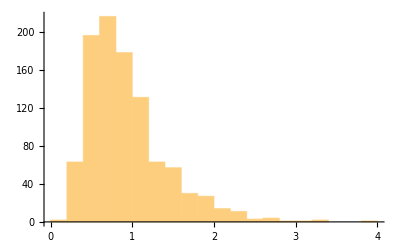

```mathematica
Histogram[Table[GeometricMean[RandomChoice[{.5,.5}->#]&/@data]^282,{n,1,1000,1}]]
```

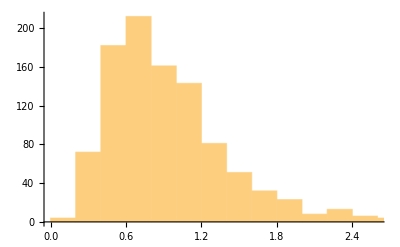

```mathematica
With[{p=.5},
Histogram[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

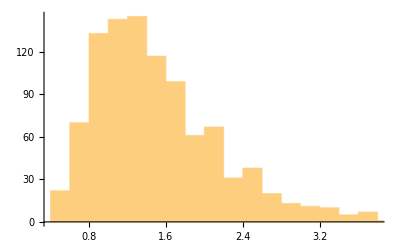

```mathematica
With[{p=.75},
Histogram[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

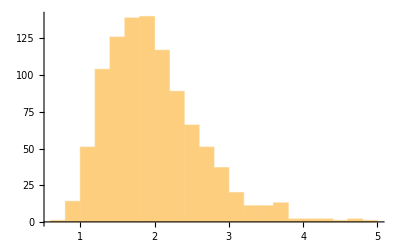

```mathematica
With[{p=.90},
Histogram[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

```mathematica
With[{p=.90},
Mean[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

1.9653

```mathematica
PercentForm@Out@47
```

196.5%

```mathematica
With[{p=.90},
PercentForm@
Mean[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

191.9%

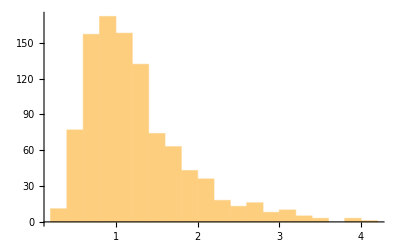

```mathematica
With[{p=.650},
Histogram[
Table[
GeometricMean[RandomChoice[{p,1-p}->#]&/@data]^282,
{n,1,1000,1}]
]
]
```

```mathematica
Manipulate[
Histogram[
Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,1000,1}]
]
,{p,0,100,1}]
```

```mathematica
Manipulate[
Histogram[
Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]
]
,{p,0,100,1}]
```

```mathematica
Manipulate[
Histogram[
Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]
,PlotRange->{{0,5},{0,100}}]
,{p,0,100,1}]
```

```mathematica
Table[
{p,
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282},
{p,1,100,1}]
```

{{1,0.292683},{2,0.286564},{3,0.324331},{4,0.321249},{5,0.207884},{6,0.39437},{7,0.352327},{8,0.357024},{9,0.360217},{10,0.531089},{11,0.240776},{12,0.661548},{13,0.309906},{14,0.299432},{15,0.297638},{16,0.357281},{17,0.623666},{18,0.392689},{19,0.37437},{20,0.630355},{21,0.448881},{22,0.564728},{23,0.55214},{24,0.794767},{25,0.304887},{26,0.337745},{27,0.74412},{28,0.349373},{29,0.37159},{30,0.447421},{31,0.995531},{32,0.28987},{33,0.51167},{34,0.679942},{35,0.489089},{36,0.885074},{37,0.449655},{38,1.9072},{39,1.42837},{40,0.299814},{41,0.348033},{42,0.480699},{43,0.609825},{44,1.14126},{45,0.704125},{46,0.563571},{47,0.968852},{48,0.683473},{49,1.53913},{50,0.574222},{51,2.61599},{52,0.602315},{53,0.516521},{54,2.92836},{55,0.685999},{56,0.575356},{57,0.675716},{58,1.5763},{59,1.35003},{60,1.03501},{61,1.10563},{62,0.926408},{63,2.43435},{64,0.491278},{65,0.710215},{66,1.05597},{67,1.95903},{68,1.02878},{69,1.38368},{70,1.345},{71,1.86021},{72,2.82791},{73,1.40152},{74,1.5886},{75,1.45968},{76,1.51596},{77,0.645903},{78,1.9063},{79,2.11062},{80,0.760914},{81,0.682721},{82,4.14209},{83,1.38189},{84,1.33363},{85,1.22315},{86,1.79},{87,1.50913},{88,0.940946},{89,2.46156},{90,2.34385},{91,2.57358},{92,2.8005},{93,2.21077},{94,2.01799},{95,2.00639},{96,3.39085},{97,1.69246},{98,2.11656},{99,2.19169},{100,2.2891}}

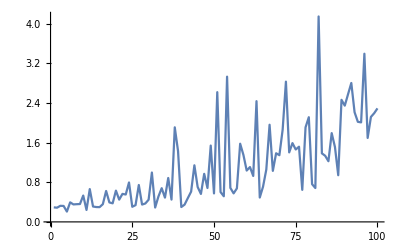

```mathematica
ListPlot[%54,Joined->True]
```

```mathematica
Table[
{p,
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282},
{p,1,100,1}]
```

```mathematica
Table[
{p,Mean@Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]}
,{p,0,100,10}]
```

{{0,0.296316},{10,0.372556},{20,0.47287},{30,0.602034},{40,0.693729},{50,1.04816},{60,1.03663},{70,1.30375},{80,1.52664},{90,2.01107},{100,2.2891}}

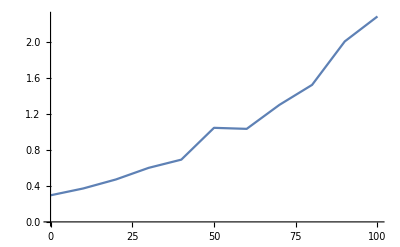

```mathematica
ListPlot[%58,Joined->True]
```

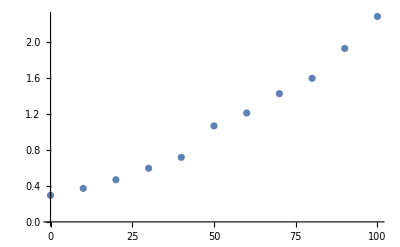

```mathematica
ListPlot@
Table[
{p,Mean@Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]}
,{p,0,100,10}]
```

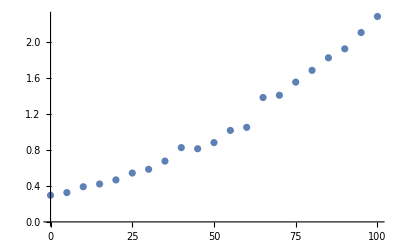

```mathematica
ListPlot@
Table[
{p,Mean@Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]}
,{p,0,100,5}]
```

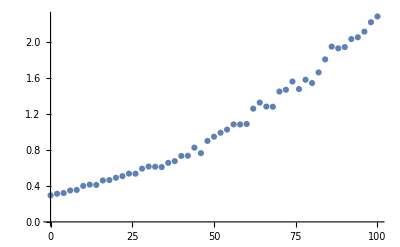

```mathematica
ListPlot@
Table[
{p,Mean@Table[
GeometricMean[RandomChoice[{p/100,1-p/100}->#]&/@data]^282,
{n,1,100,1}]}
,{p,0,100,2}]
```

```mathematica
Length@Select[First/@data,#>1&]
```

169

```mathematica
Length@Select[First/@data,#<1&]
```

112

```mathematica
Length@Select[Last/@data,#>1&]
```

109

```mathematica
Length@Select[Last/@data,#<1&]
```

173

```mathematica
Length@data
```

282

```mathematica
data
```

{{0.925903,1.04698},{1.10102,0.919684},{1.02413,0.97893},{1.02705,0.979043},{1.01473,0.976859},{1.01116,0.989636},{1.00028,0.967385},{0.981788,1.00402},{1.03457,0.955022},{1.0057,1.01806},{1.02404,0.989861},{1.03798,0.974712},{0.960864,1.09163},{1.00397,0.990373},{1.00263,0.967801},{1.02733,0.961601},{0.975448,1.04287},{0.994756,0.996244},{1.04744,0.955388},{1.02667,0.958566},{1.00074,0.990051},{1.02106,0.968468},{1.01247,0.992844},{0.996209,0.992793},{0.970749,1.03485},{1.00294,0.988074},{1.0022,0.98864},{1.03851,0.982047},{1.00868,0.996709},{0.993253,1.01798},{1.03233,0.966126},{1.00522,1.00224},{1.00587,0.961295},{0.989004,1.01007},{1.01906,0.963204},{1.00379,1.0187},{0.99756,1.00898},{0.997776,1.00155},{0.993537,0.998067},{1.01952,0.955461},{0.987679,1.02432},{0.996659,1.00633},{0.980778,1.02556},{0.975843,1.04141},{0.993227,1.00589},{1.04397,0.927526},{1.01059,0.970797},{1.01984,0.989837},{0.997596,0.984394},{1.0149,0.980392},{1.00971,1.00255},{1.00171,1.00806},{0.98997,1.00926},{1.03298,0.984981},{0.942821,1.11605},{0.996459,1.0019},{1.02243,0.946591},{0.98501,1.01521},{1.01169,0.978321},{1.0194,0.967768},{1.03422,0.983347},{1.00103,0.997036},{1.00496,1.00722},{1.0074,0.991568},{1.01326,0.978316},{1.00302,0.995654},{0.983939,1.03536},{1.0102,0.973019},{0.999192,0.97877},{1.01981,0.953962},{0.998018,0.988399},{1.00159,0.993427},{0.992068,1.00567},{1.0054,0.983553},{1.00179,0.991878},{1.02699,0.991329},{0.994783,1.02381},{0.997281,1.02041},{1.01325,0.967442},{1.00346,1.01394},{1.00192,1.00142},{0.978012,1.03693},{0.993157,1.00137},{1.02854,0.952576},{0.988325,1.05361},{0.950039,1.16765},{0.995312,0.980545},{0.992218,0.998809},{1.01073,0.922527},{0.926281,1.14599},{1.02535,0.946261},{1.01763,0.958697},{1.02726,0.957747},{0.981695,1.01384},{0.979258,1.01493},{1.02674,0.950399},{0.991248,0.988943},{0.964684,1.06619},{1.0037,0.979866},{0.972644,1.02954},{0.979464,1.01996},{1.00843,0.979209},{0.960904,1.04371},{0.990122,1.00638},{1.06485,0.946096},{1.02588,0.978634},{1.01957,0.980308},{1.02922,1.0083},{1.01347,0.990039},{0.999387,1.0035},{0.994885,0.993897},{1.01254,0.995614},{0.995329,0.990308},{1.00204,0.988434},{1.02912,0.992349},{1.0089,0.965533},{1.02785,1.0047},{0.99523,1.02384},{0.996166,0.989954},{0.964396,1.02721},{0.997805,0.99057},{1.0094,0.983228},{1.01744,0.98663},{1.02356,0.942523},{1.00913,0.962816},{1.02244,0.994851},{0.995574,1.00362},{0.985923,1.02682},{1.00282,1.00402},{1.01442,0.968985},{1.00591,0.982963},{1.01267,0.982143},{1.00127,0.999465},{0.989317,1.00321},{0.981149,1.02293},{1.01045,0.991137},{0.981724,1.01105},{1.00752,0.979188},{1.02146,0.965994},{1.01407,0.973597},{0.984865,1.03164},{1.01976,0.974808},{0.994977,1.00674},{0.993509,1.02511},{0.965336,1.05607},{0.974243,1.07732},{0.977808,1.00718},{0.910401,1.14727},{1.04054,0.936646},{1.00188,1.00442},{1.05718,0.939701},{0.978167,1.03747},{0.964408,1.07269},{1.04691,0.925084},{0.910775,1.14013},{1.00809,0.975259},{1.04295,0.944353},{1.03598,0.925043},{0.977314,1.02389},{1.02465,0.952424},{0.997795,1.01585},{0.92385,1.12435},{1.03241,0.973507},{0.987992,1.01814},{1.02111,0.97709},{1.03738,0.959618},{0.999195,1.0009},{0.982675,1.05018},{1.03239,0.93672},{1.03892,0.960937},{1.00229,0.97274},{1.00038,0.989184},{1.00114,0.999006},{1.02094,0.980597},{1.00895,0.976154},{0.997412,0.984927},{0.991475,1.01583},{1.00654,0.995844},{1.00223,0.966615},{0.999629,0.982731},{0.983503,1.04833},{1.00151,0.993714},{0.975348,1.04639},{1.01833,0.978338},{0.9928,1.00669},{0.983206,1.02762},{1.01533,0.971628},{0.963296,1.04355},{0.948204,1.06775},{1.0226,0.962759},{1.04011,0.945081},{0.986619,1.01061},{0.954926,1.0795},{1.02611,0.962946},{1.02198,0.967773},{1.03027,0.942843},{0.997294,0.965735},{1.02908,0.972162},{0.994726,0.987086},{1.0072,0.995449},{0.987028,0.998286},{1.02171,0.973097},{0.988628,1.01529},{1.00943,0.987833},{1.00374,0.98651},{1.01359,0.966112},{1.01598,1.01108},{0.998373,0.999391},{1.00905,0.974421},{0.99103,1.01625},{1.02824,0.95449},{1.01144,1.00258},{0.996693,1.01992},{1.00122,0.995589},{1.01081,0.990506},{1.00587,0.978914},{0.994339,0.997389},{1.00569,0.98822},{1.00137,1.00662},{1.00463,0.984868},{1.02149,0.95658},{1.00083,0.998603},{0.999166,1.01049},{0.989482,1.00969},{0.995276,1.00206},{1.00576,0.971272},{1.02292,0.955634},{1.00659,0.986735},{1.01293,0.995519},{0.989334,1.0165},{0.973701,1.05609},{0.979366,1.0573},{1.0185,0.953734},{1.00673,0.987526},{1.02589,0.966316},{0.99137,1.05084},{0.996386,1.00069},{1.00841,0.979972},{1.02567,0.942918},{1.00096,0.955157},{1.02086,0.977308},{1.00031,0.991994},{1.,1.0113},{1.01263,0.975259},{1.01463,1.01064},{0.998027,1.00486},{1.0003,0.989525},{1.0152,0.997557},{0.999401,1.02204},{0.982469,1.03594},{1.00778,0.958365},{1.02769,0.961384},{0.975998,1.05021},{1.01162,0.988048},{0.992394,0.995968},{1.01533,0.980567},{1.02028,0.964162},{0.99057,0.994347},{1.02168,0.973299},{0.994553,0.99469},{1.00706,0.995552},{1.02347,0.976765},{1.01035,1.00274},{0.992803,1.00639},{1.00153,1.00635},{1.00264,0.997297},{0.972512,1.05781},{0.952177,1.10333},{1.03058,0.943498},{0.998254,1.00082},{1.00933,0.984426},{0.945712,1.11324},{1.02122,0.962603},{1.04664,0.94561},{1.03342,0.960559},{1.01078,0.99059},{0.983317,1.01295},{1.02169,0.988917},{1.00612,1.00172},{1.01867,0.951807},{0.996946,1.01718},{1.00413,0.986667}}

```mathematica
Length@data
```

282

```mathematica
max=Max/@data
```

{1.04698,1.10102,1.02413,1.02705,1.01473,1.01116,1.00028,1.00402,1.03457,1.01806,1.02404,1.03798,1.09163,1.00397,1.00263,1.02733,1.04287,0.996244,1.04744,1.02667,1.00074,1.02106,1.01247,0.996209,1.03485,1.00294,1.0022,1.03851,1.00868,1.01798,1.03233,1.00522,1.00587,1.01007,1.01906,1.0187,1.00898,1.00155,0.998067,1.01952,1.02432,1.00633,1.02556,1.04141,1.00589,1.04397,1.01059,1.01984,0.997596,1.0149,1.00971,1.00806,1.00926,1.03298,1.11605,1.0019,1.02243,1.01521,1.01169,1.0194,1.03422,1.00103,1.00722,1.0074,1.01326,1.00302,1.03536,1.0102,0.999192,1.01981,0.998018,1.00159,1.00567,1.0054,1.00179,1.02699,1.02381,1.02041,1.01325,1.01394,1.00192,1.03693,1.00137,1.02854,1.05361,1.16765,0.995312,0.998809,1.01073,1.14599,1.02535,1.01763,1.02726,1.01384,1.01493,1.02674,0.991248,1.06619,1.0037,1.02954,1.01996,1.00843,1.04371,1.00638,1.06485,1.02588,1.01957,1.02922,1.01347,1.0035,0.994885,1.01254,0.995329,1.00204,1.02912,1.0089,1.02785,1.02384,0.996166,1.02721,0.997805,1.0094,1.01744,1.02356,1.00913,1.02244,1.00362,1.02682,1.00402,1.01442,1.00591,1.01267,1.00127,1.00321,1.02293,1.01045,1.01105,1.00752,1.02146,1.01407,1.03164,1.01976,1.00674,1.02511,1.05607,1.07732,1.00718,1.14727,1.04054,1.00442,1.05718,1.03747,1.07269,1.04691,1.14013,1.00809,1.04295,1.03598,1.02389,1.02465,1.01585,1.12435,1.03241,1.01814,1.02111,1.03738,1.0009,1.05018,1.03239,1.03892,1.00229,1.00038,1.00114,1.02094,1.00895,0.997412,1.01583,1.00654,1.00223,0.999629,1.04833,1.00151,1.04639,1.01833,1.00669,1.02762,1.01533,1.04355,1.06775,1.0226,1.04011,1.01061,1.0795,1.02611,1.02198,1.03027,0.997294,1.02908,0.994726,1.0072,0.998286,1.02171,1.01529,1.00943,1.00374,1.01359,1.01598,0.999391,1.00905,1.01625,1.02824,1.01144,1.01992,1.00122,1.01081,1.00587,0.997389,1.00569,1.00662,1.00463,1.02149,1.00083,1.01049,1.00969,1.00206,1.00576,1.02292,1.00659,1.01293,1.0165,1.05609,1.0573,1.0185,1.00673,1.02589,1.05084,1.00069,1.00841,1.02567,1.00096,1.02086,1.00031,1.0113,1.01263,1.01463,1.00486,1.0003,1.0152,1.02204,1.03594,1.00778,1.02769,1.05021,1.01162,0.995968,1.01533,1.02028,0.994347,1.02168,0.99469,1.00706,1.02347,1.01035,1.00639,1.00635,1.00264,1.05781,1.10333,1.03058,1.00082,1.00933,1.11324,1.02122,1.04664,1.03342,1.01078,1.01295,1.02169,1.00612,1.01867,1.01718,1.00413}

```mathematica
Map[
Apply[Equal,#]&
,Transpose[{
First/@data,
Max/@data
}]]
```

{False,True,True,True,True,True,True,False,True,False,True,True,False,True,True,True,False,False,True,True,True,True,True,True,False,True,True,True,True,False,True,True,True,False,True,False,False,False,False,True,False,False,False,False,False,True,True,True,True,True,True,False,False,True,False,False,True,False,True,True,True,True,False,True,True,True,False,True,True,True,True,True,False,True,True,True,False,False,True,False,True,False,False,True,False,False,True,False,True,False,True,True,True,False,False,True,True,False,True,False,False,True,False,False,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,False,True,True,True,True,True,True,False,False,False,True,True,True,True,False,False,True,False,True,True,True,False,True,False,False,False,False,False,False,True,False,True,False,False,True,False,True,True,True,False,True,False,False,True,False,True,True,False,False,True,True,True,True,True,True,True,True,False,True,True,True,False,True,False,True,False,False,True,False,False,True,True,False,False,True,True,True,True,True,True,True,False,True,False,True,True,True,True,False,True,False,True,True,False,True,True,True,False,True,False,True,True,True,False,False,False,True,True,True,True,False,False,False,True,True,True,False,False,True,True,True,True,True,False,True,True,False,True,True,False,False,True,True,False,True,False,True,True,False,True,False,True,True,True,False,False,True,False,False,True,False,True,False,True,True,True,True,False,True,True,True,False,True}

```mathematica
Count[
Map[
Apply[Equal,#]&
,Transpose[{
First/@data,
Max/@data
}]],
True]
```

174

```mathematica
Count[
Map[
Apply[Equal,#]&
,Transpose[{
First/@data,
Max/@data
}]],
True]
```

174

```mathematica
GeometricMean[First/@data]
```

1.00294

```mathematica
GeometricMean[First/@data]^(Length@data)
```

2.2891

```mathematica
PercentForm[GeometricMean[First/@data]^(Length@data)]
```

228.9%

```mathematica
Count[
Map[
Apply[Equal,#]&
,Transpose[{
Last/@data,
Max/@data
}]],
True]
```

108

```mathematica
PercentForm[Count[
Map[
Apply[Equal,#]&
,Transpose[{
First/@data,
Max/@data
}]],
True]/(Length@data)]
```

29/47

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
First/@data,
Max/@data
}]],
True]/(Length@data))]
```

61.7%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
Last/@data,
Max/@data
}]],
True]/(Length@data))]
```

38.3%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

59.93%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

61.35%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

58.16%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

58.51%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

58.87%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

60.28%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

56.38%

```mathematica
PercentForm[N@(Count[
Map[
Apply[Equal,#]&
,Transpose[{
RandomChoice[{.9,.1}->#]&/@data,
Max/@data
}]],
True]/(Length@data))]
```

58.51%